# Bernoulli example

### Define the working directory and load CmdStan.m

```mathematica
(* Linux *)
SetDirectory["~/GitHub/MathematicaStan/Examples/Bernoulli/"]

(* Windows *)
(* SetDirectory["C:\\Users\\USER_NAME\\Documents\\Mathematica\\STAN\\Examples\\Bernoulli"] *)

Needs["CmdStan`"]
```

/IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli

### Generate the Bernoulli Stan code and compile it

```mathematica
stanCode="data { 
  int<lower=0> N; 
  int<lower=0,upper=1> y[N];
} 
parameters {
  real<lower=0,upper=1> theta;
} 
model {
  theta ~ beta(1,1);
  for (n in 1:N) 
    y[n] ~ bernoulli(theta);
}";
StanCodeExport["bernoulli",stanCode]

(* Compile your code.
 * Caveat: this can take some time
 *)
StanCompile["bernoulli"]
```

bernoulli.stan

make: '/IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli' is up to date.

### Generate some data and save them (RDump file)

```mathematica
n=5000;
y=Table[Random[BernoulliDistribution[0.2016]],{i,1,n}];

RDumpExport["bernoulli",{{"N",n},{"y",y}}];
```

### Run Stan and get result

#### Use sample method (ONE job)

```mathematica
StanRunSample["bernoulli"]

output=StanImport["output.csv"];
```

method = sample (Default)
  sample
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default)
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      gamma = 0.050000000000000003 (Default)
      delta = 0.80000000000000004 (Default)
      kappa = 0.75 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
    algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 10 (Default)
        metric = diag_e (Default)
        stepsize = 1 (Default)
        stepsize_jitter = 0 (Default)
id = 0 (Default)
data
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
init = 2 (Default)
random
  seed = 3919364410
output
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/output.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)


Gradient evaluation took 0.000399 seconds
1000 transitions using 10 leapfrog steps per transition would take 3.99 seconds.
Adjust your expectations accordingly!


Iteration:    1 / 2000 [  0%]  (Warmup)
Iteration:  100 / 2000 [  5%]  (Warmup)
Iteration:  200 / 2000 [ 10%]  (Warmup)
Iteration:  300 / 2000 [ 15%]  (Warmup)
Iteration:  400 / 2000 [ 20%]  (Warmup)
Iteration:  500 / 2000 [ 25%]  (Warmup)
Iteration:  600 / 2000 [ 30%]  (Warmup)
Iteration:  700 / 2000 [ 35%]  (Warmup)
Iteration:  800 / 2000 [ 40%]  (Warmup)
Iteration:  900 / 2000 [ 45%]  (Warmup)
Iteration: 1000 / 2000 [ 50%]  (Warmup)
Iteration: 1001 / 2000 [ 50%]  (Sampling)
Iteration: 1100 / 2000 [ 55%]  (Sampling)
Iteration: 1200 / 2000 [ 60%]  (Sampling)
Iteration: 1300 / 2000 [ 65%]  (Sampling)
Iteration: 1400 / 2000 [ 70%]  (Sampling)
Iteration: 1500 / 2000 [ 75%]  (Sampling)
Iteration: 1600 / 2000 [ 80%]  (Sampling)
Iteration: 1700 / 2000 [ 85%]  (Sampling)
Iteration: 1800 / 2000 [ 90%]  (Sampling)
Iteration: 1900 / 2000 [ 95%]  (Sampling)
Iteration: 2000 / 2000 [100%]  (Sampling)

 Elapsed Time: 1.47087 seconds (Warm-up)
               1.7528 seconds (Sampling)
               3.22366 seconds (Total)

### Use the results

#### List Header

```mathematica
StanImportHeader[output]
```

{{lp__,1},{accept_stat__,2},{stepsize__,3},{treedepth__,4},{n_leapfrog__,5},{divergent__,6},{energy__,7},{theta,8}}

#### Show sample matrix

```mathematica
Dimensions[StanImportData[output]]
Take[StanImportData[output],3]
```

{1000,8}

{{-2508.15,0.574074,1.5896,1.,1.,0.,2509.9,0.203886},{-2508.34,0.948844,1.5896,1.,3.,0.,2508.41,0.196025},{-2508.47,0.969459,1.5896,1.,3.,0.,2508.61,0.206291}}

#### Plot θ sample and histogram

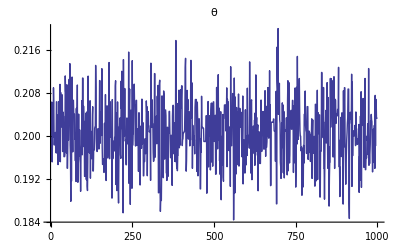

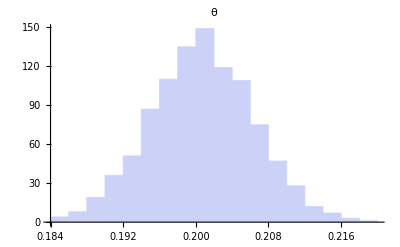

```mathematica
ListLinePlot[Flatten[StanVariableColumn["theta",output]],PlotLabel->"θ"]
Histogram[Flatten[StanVariableColumn["theta",output]],PlotLabel->"θ"]
```

### Maximimize likelihood with StanRunOptimize

```mathematica
StanRunOptimize["bernoulli"]
```

method = optimize
  optimize
    algorithm = lbfgs (Default)
      lbfgs
        init_alpha = 0.001 (Default)
        tol_obj = 9.9999999999999998e-13 (Default)
        tol_rel_obj = 10000 (Default)
        tol_grad = 1e-08 (Default)
        tol_rel_grad = 10000000 (Default)
        tol_param = 1e-08 (Default)
        history_size = 5 (Default)
    iter = 2000 (Default)
    save_iterations = 0 (Default)
id = 0 (Default)
data
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
init = 2 (Default)
random
  seed = 3919368427
output
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/output.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)

initial log joint probability = -2513.39
    Iter      log prob        ||dx||      ||grad||       alpha      alpha0  # evals  Notes 
       3      -2506.17    0.00131072     0.0238056      0.9687      0.9687        4   
Optimization terminated normally: 
  Convergence detected: relative gradient magnitude is below tolerance

#### Options manipulation

```mathematica
StanSetOptionOptimize["output.file","output_optimize.csv"];    
StanSetOptionOptimize["method.optimize.iter",100];                    
StanSetOptionOptimize["method.optimize.algorithm","bfgs"];
StanSetOptionOptimize["method.optimize.algorithm.bfgs.tol_grad",10.^-5];
StanOptionOptimize[] 

(* re-run the solver with the new options *)
StanRunOptimize["bernoulli"]
```

{{method.optimize.algorithm.bfgs.tol_grad,0.00001},{method.optimize.algorithm,bfgs},{method.optimize.iter,100},{output.file,output_optimize.csv}}

method = optimize
  optimize
    algorithm = bfgs
      bfgs
        init_alpha = 0.001 (Default)
        tol_obj = 9.9999999999999998e-13 (Default)
        tol_rel_obj = 10000 (Default)
        tol_grad = 1.0000000000000001e-05
        tol_rel_grad = 10000000 (Default)
        tol_param = 1e-08 (Default)
    iter = 100
    save_iterations = 0 (Default)
id = 0 (Default)
data
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
init = 2 (Default)
random
  seed = 3919368500
output
  file = output_optimize.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)

initial log joint probability = -2517.89
    Iter      log prob        ||dx||      ||grad||       alpha      alpha0  # evals  Notes 
       3      -2506.17    0.00210032     0.0535299      0.9571      0.9571        4   
Optimization terminated normally: 
  Convergence detected: relative gradient magnitude is below tolerance

#### Overwrite and/or reset option

```mathematica
StanOptionOptimize[]
StanSetOptionOptimize["method.optimize.iter",2016];  
StanOptionOptimize[]
```

{{method.optimize.algorithm.bfgs.tol_grad,0.00001},{method.optimize.algorithm,bfgs},{method.optimize.iter,100},{output.file,output_optimize.csv}}

{{method.optimize.algorithm.bfgs.tol_grad,0.00001},{method.optimize.algorithm,bfgs},{method.optimize.iter,2016},{output.file,output_optimize.csv}}

#### Remove all method* options

```mathematica
StanOptionOptimize[]
StanRemoveOptionOptimize["method*"];  
StanOptionOptimize[]
```

{{method.optimize.algorithm.bfgs.tol_grad,0.00001},{method.optimize.algorithm,bfgs},{method.optimize.iter,2016},{output.file,output_optimize.csv}}

{{output.file,output_optimize.csv}}

#### Erase all options

```mathematica
StanOptionOptimize[]
StanResetOptionOptimize[];
StanOptionOptimize[]
```

{{output.file,output_optimize.csv}}

{}

### Parallel Sampling

#### Redo the previous computation with 4 jobs in parallel (ONLY works under Linux for the moment)

method = sample (Default)
  sample
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default)
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      gamma = 0.050000000000000003 (Default)
      delta = 0.80000000000000004 (Default)
      kappa = 0.75 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
    algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 10 (Default)
        metric = diag_e (Default)
        stepsize = 1 (Default)
        stepsize_jitter = 0 (Default)
id = 2
data
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
init = 2 (Default)
random
  seed = 3919368663
output
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/output_2.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)


Gradient evaluation took 0.000377 seconds
1000 transitions using 10 leapfrog steps per transition would take 3.77 seconds.
Adjust your expectations accordingly!


method = sample (Default)
  sample
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default)
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      gamma = 0.050000000000000003 (Default)
      delta = 0.80000000000000004 (Default)
      kappa = 0.75 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
    algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 10 (Default)
        metric = diag_e (Default)
        stepsize = 1 (Default)
        stepsize_jitter = 0 (Default)
id = 4
data
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
init = 2 (Default)
random
  seed = 3919368665
output
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/output_4.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)

method = sample (Default)
  sample
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default)
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      gamma = 0.050000000000000003 (Default)
method = sample (Default)
  sample
      delta = 0.80000000000000004 (Default)
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default)
      kappa = 0.75 (Default)
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
      gamma = 0.050000000000000003 (Default)
    algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
      delta = 0.80000000000000004 (Default)
            max_depth = 10 (Default)
        metric = diag_e (Default)
      kappa = 0.75 (Default)
        stepsize = 1 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
        stepsize_jitter = 0 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
id = 3
data
    algorithm = hmc (Default)
      hmc
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
        engine = nuts (Default)
init = 2 (Default)
          nuts
random
            max_depth = 10 (Default)
  seed = 3919368665
output
        metric = diag_e (Default)
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/output_3.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)
        stepsize = 1 (Default)

        stepsize_jitter = 0 (Default)
id = 1
data
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
init = 2 (Default)
random
  seed = 3919368665
output
  file = /IS006139/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/output_1.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)


Gradient evaluation took 0.000555 seconds
1000 transitions using 10 leapfrog steps per transition would take 5.55 seconds.
Adjust your expectations accordingly!




Gradient evaluation took 0.000635 seconds
Gradient evaluation took 0.000633 seconds
1000 transitions using 10 leapfrog steps per transition would take 6.35 seconds.
1000 transitions using 10 leapfrog steps per transition would take 6.33 seconds.
Adjust your expectations accordingly!
Adjust your expectations accordingly!




Iteration:    1 / 2000 [  0%]  (Warmup)
Iteration:    1 / 2000 [  0%]  (Warmup)
Iteration:    1 / 2000 [  0%]  (Warmup)
Iteration:    1 / 2000 [  0%]  (Warmup)
Iteration:  100 / 2000 [  5%]  (Warmup)
Iteration:  100 / 2000 [  5%]  (Warmup)
Iteration:  100 / 2000 [  5%]  (Warmup)
Iteration:  100 / 2000 [  5%]  (Warmup)
Iteration:  200 / 2000 [ 10%]  (Warmup)
Iteration:  200 / 2000 [ 10%]  (Warmup)
Iteration:  200 / 2000 [ 10%]  (Warmup)
Iteration:  200 / 2000 [ 10%]  (Warmup)
Iteration:  300 / 2000 [ 15%]  (Warmup)
Iteration:  300 / 2000 [ 15%]  (Warmup)
Iteration:  300 / 2000 [ 15%]  (Warmup)
Iteration:  300 / 2000 [ 15%]  (Warmup)
Iteration:  400 / 2000 [ 20%]  (Warmup)
Iteration:  400 / 2000 [ 20%]  (Warmup)
Iteration:  400 / 2000 [ 20%]  (Warmup)
Iteration:  400 / 2000 [ 20%]  (Warmup)
Iteration:  500 / 2000 [ 25%]  (Warmup)
Iteration:  500 / 2000 [ 25%]  (Warmup)
Iteration:  500 / 2000 [ 25%]  (Warmup)
Iteration:  500 / 2000 [ 25%]  (Warmup)
Iteration:  600 / 2000 [ 30%]  (Warmup)
Iteration:  600 / 2000 [ 30%]  (Warmup)
Iteration:  600 / 2000 [ 30%]  (Warmup)
Iteration:  600 / 2000 [ 30%]  (Warmup)
Iteration:  700 / 2000 [ 35%]  (Warmup)
Iteration:  700 / 2000 [ 35%]  (Warmup)
Iteration:  700 / 2000 [ 35%]  (Warmup)
Iteration:  700 / 2000 [ 35%]  (Warmup)
Iteration:  800 / 2000 [ 40%]  (Warmup)
Iteration:  800 / 2000 [ 40%]  (Warmup)
Iteration:  800 / 2000 [ 40%]  (Warmup)
Iteration:  800 / 2000 [ 40%]  (Warmup)
Iteration:  900 / 2000 [ 45%]  (Warmup)
Iteration:  900 / 2000 [ 45%]  (Warmup)
Iteration:  900 / 2000 [ 45%]  (Warmup)
Iteration:  900 / 2000 [ 45%]  (Warmup)
Iteration: 1000 / 2000 [ 50%]  (Warmup)
Iteration: 1001 / 2000 [ 50%]  (Sampling)
Iteration: 1000 / 2000 [ 50%]  (Warmup)
Iteration: 1001 / 2000 [ 50%]  (Sampling)
Iteration: 1000 / 2000 [ 50%]  (Warmup)
Iteration: 1000 / 2000 [ 50%]  (Warmup)
Iteration: 1001 / 2000 [ 50%]  (Sampling)
Iteration: 1001 / 2000 [ 50%]  (Sampling)
Iteration: 1100 / 2000 [ 55%]  (Sampling)
Iteration: 1100 / 2000 [ 55%]  (Sampling)
Iteration: 1100 / 2000 [ 55%]  (Sampling)
Iteration: 1100 / 2000 [ 55%]  (Sampling)
Iteration: 1200 / 2000 [ 60%]  (Sampling)
Iteration: 1200 / 2000 [ 60%]  (Sampling)
Iteration: 1200 / 2000 [ 60%]  (Sampling)
Iteration: 1200 / 2000 [ 60%]  (Sampling)
Iteration: 1300 / 2000 [ 65%]  (Sampling)
Iteration: 1300 / 2000 [ 65%]  (Sampling)
Iteration: 1300 / 2000 [ 65%]  (Sampling)
Iteration: 1400 / 2000 [ 70%]  (Sampling)
Iteration: 1300 / 2000 [ 65%]  (Sampling)
Iteration: 1400 / 2000 [ 70%]  (Sampling)
Iteration: 1400 / 2000 [ 70%]  (Sampling)
Iteration: 1500 / 2000 [ 75%]  (Sampling)
Iteration: 1400 / 2000 [ 70%]  (Sampling)
Iteration: 1500 / 2000 [ 75%]  (Sampling)
Iteration: 1600 / 2000 [ 80%]  (Sampling)
Iteration: 1500 / 2000 [ 75%]  (Sampling)
Iteration: 1500 / 2000 [ 75%]  (Sampling)
Iteration: 1600 / 2000 [ 80%]  (Sampling)
Iteration: 1700 / 2000 [ 85%]  (Sampling)
Iteration: 1600 / 2000 [ 80%]  (Sampling)
Iteration: 1600 / 2000 [ 80%]  (Sampling)
Iteration: 1800 / 2000 [ 90%]  (Sampling)
Iteration: 1700 / 2000 [ 85%]  (Sampling)
Iteration: 1700 / 2000 [ 85%]  (Sampling)
Iteration: 1700 / 2000 [ 85%]  (Sampling)
Iteration: 1900 / 2000 [ 95%]  (Sampling)
Iteration: 1800 / 2000 [ 90%]  (Sampling)
Iteration: 1800 / 2000 [ 90%]  (Sampling)
Iteration: 2000 / 2000 [100%]  (Sampling)

 Elapsed Time: 1.66671 seconds (Warm-up)
               1.50367 seconds (Sampling)
               3.17038 seconds (Total)

Iteration: 1800 / 2000 [ 90%]  (Sampling)
Iteration: 1900 / 2000 [ 95%]  (Sampling)
Iteration: 2000 / 2000 [100%]  (Sampling)

 Elapsed Time: 1.72077 seconds (Warm-up)
               1.60987 seconds (Sampling)
               3.33064 seconds (Total)

Iteration: 1900 / 2000 [ 95%]  (Sampling)
Iteration: 1900 / 2000 [ 95%]  (Sampling)
Iteration: 2000 / 2000 [100%]  (Sampling)

 Elapsed Time: 1.7269 seconds (Warm-up)
               1.80656 seconds (Sampling)
               3.53347 seconds (Total)

Iteration: 2000 / 2000 [100%]  (Sampling)

 Elapsed Time: 1.69561 seconds (Warm-up)
               1.82515 seconds (Sampling)
               3.52076 seconds (Total)

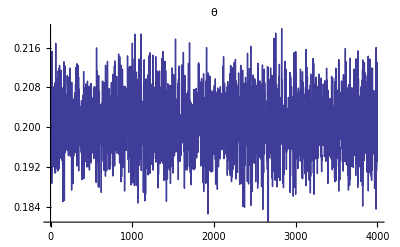

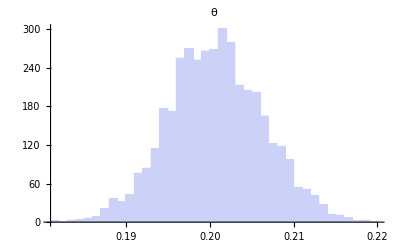

```mathematica
StanRunSample["bernoulli",4]  (* 4 jobs *)
output=StanImport["output.csv"];
ListLinePlot[Flatten[StanVariableColumn["theta",output]],PlotLabel->"θ"]
Histogram[Flatten[StanVariableColumn["theta",output]],PlotLabel->"θ"]
```